1, p. 343.

Somas de termos trigonométricos do tipo

a_1 cos(n t+ϵ_1)+a_2 cos(2n t+ϵ_2)+a_3 cos(3n t+ϵ_3)+...

Sendo t o tempo, mas irrelevante; ϵ a fase.

O termo é:

a cos(b x+c)

```mathematica
Manipulate[Plot[a Cos[b x+c],{x,-50,50},PlotRange->{-1.1,1.1},ImageSize->250],{{a,1},.1,2,.1},{{b,1},.1,1,.1},{{c,0},-1,1,.1}]
```

a amplitude, b período, c fase.

Eixo x é o tempo; por isso a expressão (0.1) é uma função de x.

(Diz que a corresponde à posição na corda de um instrumento ou barra de um diapasão.)

ϵ_n então é irrelevante, pois é só um deslocamento.

(Tratando a como irrelevante pois não é o que muda.)

Diapasão:

a_1 cos(n_1 t+ϵ_1)+a_2 cos(n_2 t+ϵ_2)+a_3 cos(n_3 t+e_3)+...

Aqui, a diferença é a evolução de n_n, que é o período em função do tempo. Onde em (0.1), era uma evolução linear e agora não é; por isso, a função como um todo não mais é periódica sobre t. Mas é constituída por elementos que são, cada termo somado.

A questão é a soma de funções trigonométricas, cada uma com um período independente da outra. (Ou seja, n_n é arbitrário.)

```mathematica
Simplify[Cos[x]+Cos[1.4x]+Cos[3x]]
```

Cos[x]+Cos[1.4 x]+Cos[3 x]

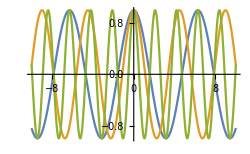

```mathematica
Plot[{Cos[x],Cos[1.4x],Cos[3x]},{x,-10,10},ImageSize->250]
```

```mathematica
Manipulate[Plot[Cos[b1 x]+Cos[b2 x]+Cos[b3 x],{x,-10,10},PlotRange->{-3.1,3.1},ImageSize->250],{{b1,1},.1,10,.1},{{b2,4.9},.1,10,.1},{{b3,9.2},.1,10,.1}]
```

E no caso anterior, dos períodos apenas múltiplos entre si...

```mathematica
Manipulate[Plot[Cos[b x]+Cos[2 b x]+Cos[4 b x],{x,-10,10},PlotRange->{-2,3.1},ImageSize->250],{{b,1},.1,10,.1}]
```

{b1→{7.2421},b2→{0.67316},b3→{4.5302}}

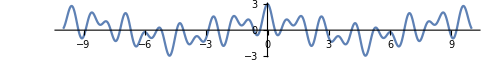

{b1→{5.17073},b2→{5.33787},b3→{5.23905}}

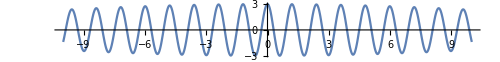

{b1→{1.87622},b2→{5.33017},b3→{4.71264}}

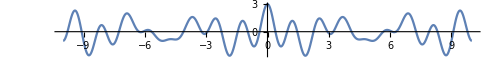

{b1→{3.42831},b2→{4.93033},b3→{3.02541}}

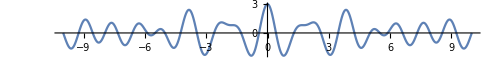

{b1→{3.47277},b2→{-1.51719},b3→{8.68621}}

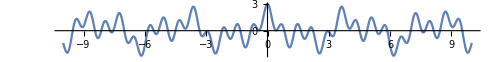

{b1→{3.57553},b2→{8.62765},b3→{3.3102}}

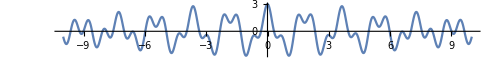

{b1→{5.38679},b2→{3.45954},b3→{3.18275}}

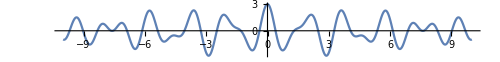

{b1→{9.74385},b2→{7.78252},b3→{5.63946}}

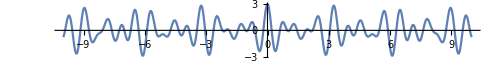

{b1→{4.12044},b2→{4.40715},b3→{6.16591}}

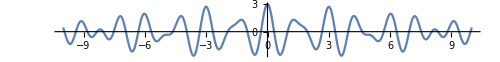

{b1→{3.54577},b2→{-0.0165038},b3→{7.13112}}

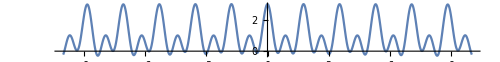

```mathematica
Module[{values,getValue},
getValue=Function[,RandomVariate[NormalDistribution[5,2.5],1]];
Column[Table[
values={b1->getValue[],b2->getValue[],b3->getValue[]};
Print[values];
Print[Plot[Cos[b1 x]+Cos[b2 x]+Cos[b3 x]/.values,{x,-10,10},ImageSize->500,AspectRatio->1/8]];
,10]]
]
```

1. {b1→1,b2→2,b3→3}

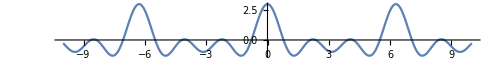

2. {b1→1,b2→2,b3→4}

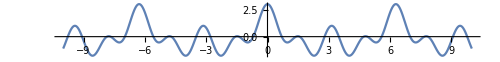

3. {b1→1,b2→3,b3→4}

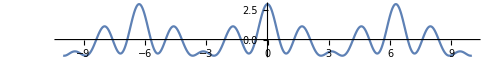

4. {b1→1,b2→3,b3→5}

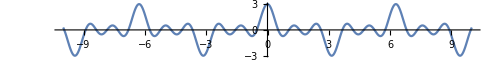

5. {b1→1,b2→3,b3→8}

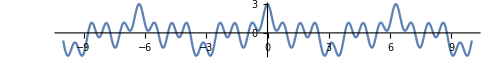

6. {b1→1,b2→3,b3→9}

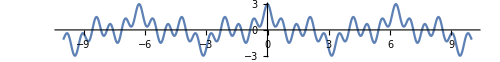

7. {b1→2,b2→3,b3→4}

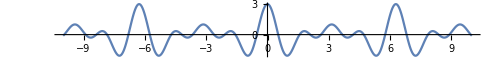

8. {b1→2,b2→4,b3→6}

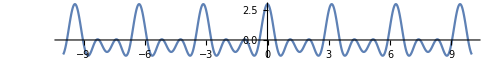

```mathematica
Module[{i,vals},
i=1;
vals={
{b1->1,b2->2,b3->3},
{b1->1,b2->2,b3->4},
{b1->1,b2->3,b3->4},
{b1->1,b2->3,b3->5},
{b1->1,b2->3,b3->8},
{b1->1,b2->3,b3->9},
{b1->2,b2->3,b3->4},
{b1->2,b2->4,b3->6}
};
Column[Table[
Print[i,". ",values];
Print[Plot[Cos[b1 x]+Cos[b2 x]+Cos[b3 x]/.values,{x,-10,10},ImageSize->500,AspectRatio->1/8]];
i++;
,{values,vals}]]
]
```

A função (1) é periódica sobre x? E a função (2) não o é mais?

“(...) (corda de instrumento) não mais temos n_2 igual ao dobro de n_1, ou n_3 igual ao triplo de n_1; de fato, as razões n_1:n_2:n_3:... são iguais a 3.52...:22.03...:61.70...:.... A soma de uma série deste tipo não é evidentemente uma função periódica de t, mas podemos defini-la como constituída de elementos periódicos, os períodos dos quais são (2π)/n_1, (2π)/n_2, etc..”

Anyway, verificamos que a “periodicidade” permanece em dois casos, {1,2,3} e {2,4,6}, e que o motivo da periodicidade, portanto, é o incremento regular dos coeficientes. (Também na última função de coeficientes randômicos se verifica a proximidade a este resultado.)

As funções ((1), (8)) aparentemente são periódicas, sendo a fase regular, ficando apenas a amplitude variável. (E as outras não têm a fase regular? Precisava medir isso — parece que é exatamente o que o periodograma faz.)

São as outras, portanto, a que ele se refere como constituídas por termos trigonométricos independentes.

Mas se parte da observação dos dados e da tentativa de se descobrir os constituintes. Mas, desde início, incluindo o ruído na equação.

O objetivo é descobrir os períodos, para então avaliar a amplitude e fase.

### Periodicidade

Irrespectivo da série, um período proposto p produz uma sequência de restos da divisão dos inteiros por ele:

0, R(1/p),R(2/p),R(3/p),...

```mathematica
Clear[pRem];
pRem=Function[p,Table[QuotientRemainder[i,p][[1]],{i,20}]];
```

```mathematica
Column[Table[PaddedForm[p,2]->pRem[p],{p,10}]]
```

1→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}
  2→{0,1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10}
  3→{0,0,1,1,1,2,2,2,3,3,3,4,4,4,5,5,5,6,6,6}
  4→{0,0,0,1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,5}
  5→{0,0,0,0,1,1,1,1,1,2,2,2,2,2,3,3,3,3,3,4}
  6→{0,0,0,0,0,1,1,1,1,1,1,2,2,2,2,2,2,3,3,3}
  7→{0,0,0,0,0,0,1,1,1,1,1,1,1,2,2,2,2,2,2,2}
  8→{0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,2,2,2,2,2}
  9→{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,2,2,2}
 10→{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,2}

A correlação entre estas séries e os valores da série de dados.

{1.,0.877583,0.540302,0.0707372,-0.416147,-0.801144,-0.989992,-0.936457,-0.653644,-0.210796,0.283662,0.70867,0.96017,0.976588,0.753902,0.346635,-0.1455,-0.602012,-0.91113,-0.997172,-0.839072,-0.475537,0.0044257,0.483305,0.843854,0.997798,0.907447,0.594921,0.136737,-0.354924,-0.759688,-0.978453,-0.957659,-0.702397,-0.275163,0.21944,0.660317,0.939525,0.988705,0.795815,0.408082} (41)

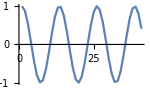

1. | 0.877583 | 0.540302 | 0.0707372 | -0.416147 | -0.801144
-0.989992 | -0.936457 | -0.653644 | -0.210796 | 0.283662 | 0.70867
0.96017 | 0.976588 | 0.753902 | 0.346635 | -0.1455 | -0.602012
-0.91113 | -0.997172 | -0.839072 | -0.475537 | 0.0044257 | 0.483305
0.843854 | 0.997798 | 0.907447 | 0.594921 | 0.136737 | -0.354924
-0.759688 | -0.978453 | -0.957659 | -0.702397 | -0.275163 | 0.21944

sums: {1.27133,-1.79856,2.28978,-2.73518,3.12583,-3.45392}

means: {0.211889,-0.299759,0.381631,-0.455863,0.520972,-0.575654}

means std. dev.: 0.465438

data std. dev.: 0.720639

correlation: 0.645868

```mathematica
Module[{data,len,parts,sums,means,meansStdDev,stdDev,corr},
	SeedRandom[1];
	data=Table[Cos[x],{x,0,20,.5}];
	len=Length[data];
	Print[data," (",len,")"];
	Print[ListLinePlot[data,ImageSize->150]];
	parts=Partition[data1,6];
	Print[Grid[parts]];
	sums=Table[Total[part],{part,parts}];
	Print["sums: ",sums];
	means=Table[Mean[part],{part,parts}];
	Print["means: ",means];
	meansStdDev=StandardDeviation[means];
	Print["means std. dev.: ",meansStdDev];
	stdDev=StandardDeviation[data];
	Print["data std. dev.: ",stdDev];
	corr=N[meansStdDev/stdDev];
	Print["correlation: ",corr];
]
```

```mathematica
Clear[corr];
corr=Function[{data,period,dbg},Module[{parts,means,meansStdDev,stdDev},
	If[dbg,Print["*period: ",period]];
	parts=Partition[data,period];
	If[dbg,Print["parts: ",parts]];
	means=Table[Mean[part],{part,parts}];
	If[dbg,Print["means: ",means]];
	meansStdDev=StandardDeviation[means];
	If[dbg,Print["meansStdDev: ",meansStdDev]];
	stdDev=StandardDeviation[data];
	If[dbg,Print["stdDev: ",stdDev]];
	N[stdDev/meansStdDev]
]];
```

```mathematica
Module[{data},
	SeedRandom[1];
	data=Table[Cos[x],{x,0,20,.5}];(*mesmo acima*)
	Table[corr[data,period,False],{period,5,15}]
]
```

{1.16258,1.5483,1.75543,2.24329,2.49994,4.30637,7.35694,86.3958,1017.75,31.8717,7.03287}

```mathematica
Clear[periodogram]
periodogram=Function[{data,periodRange,plotWidth,plotRange,dbg},Module[{periods,corrs},
	If[dbg,Print[data," (",Length[data],")"]];
	corrs=Table[corr[data,period,False],{period,periodRange}];
	If[dbg,Print["corrs: ",corrs]];
	ListLinePlot[corrs,ImageSize->plotWidth,PlotRange->plotRange,PlotTheme->"Grid"]
]];
```

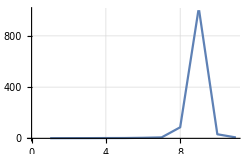

```mathematica
Module[{data},
data=Table[Cos[x],{x,0,20,.5}];
periodogram[data,Range[5,15],250,{0,1000},False]
]
```

```mathematica
Manipulate[Module[{fun,data},
fun=Function[{a,b,c,x},a Cos[b x+c]];
data=Table[fun[a,b,c,x],{x,-25,25}];
Column[{
"len(data): "<>ToString[Length[data]],Plot[fun[a,b,c,x],{x,-25,25},PlotRange->{-1.1,1.1},ImageSize->350,AspectRatio->1/2,PlotTheme->"Grid"],
periodogram[data,Range[periodFrom,periodTo],350,{0,10000},False]}
]
],
{{a,1},-2,2,.1},
{{b,0.94},.01,2,.01},
{{c,0},-5,5,.1},
{{periodFrom,1},1,25,1,Appearance->"Labeled"},{{periodTo,25},1,25,1,Appearance->"Labeled"}]
```

O período máximo válido deve ser n/2 para que haja mais de uma partição.

Quanto maior o intervalo de períodos abrangidos, maior a visualização sobre possíveis picos progressivamente maiores.

Alterar a fase altera a amplitude, mas não posição dos picos.

Alterar a amplitude (previsivelmente) não altera os picos (a não ser que ela se torne zero).

Um componente de período p (componente é um padrão na onda inteira) ao ser particionado terá a mesma fase em todas as linhas de cada coluna. A sequência das médias, portanto, formará uma onda, e sua variância será máxima. Em um componente de período ≠p, as fases diferentes formarão médias com pouca variação, pois as diferenças entre as fases, por serem em princípio “uniformes”, formarão médias com tendência à uniformidade. E portanto menos dispersas.

Dúvida. Essa oscilação de dispersão não deveria ser linear? Os picos porém são grandes.

Whittaker p. 348: “(Pela equação do periodograma) é possível observar que com um valor suficiente de m (número de linhas), o valor de correlação n é uma fração pequena, exceto quando p está próximo do período T (...) em que a curva do periodograma tem um pico de largura (2T)/m cercado por picos menores em ambos os lados.” Esta parte do Whittaker explica.

O princípio é exatamente o reproduzido abaixo (de epoch_check).

```mathematica
Manipulate[Module[{datas,mean},
datas=Table[Table[Sin[x + b*(n*.7)],{x,0,20,.2}],{n,3}];
mean=Mean/@Transpose[datas];
Column[Table[ListLinePlot[data,ImageSize->250,PlotRange->{-1,1},AspectRatio->1/4],{data,Join[datas,{mean}]}]]
],{{b,-1.5},-10,10,.05}]
```

Basicamente, o periodograma movimenta este slide de período e plota a amplitude da onda resultante × período.

Basicamente, a amplitude é um número maximizado do dado resultante quando há o alinhamento dos períodos. Mas há alguma outra situação que provoca o mesmo máximo? E que portanto falha o processo.

A equação do periodograma nesta forma é

n^2=S_M^2/σ^2

em que:

n é o coeficiente de correlação;

S_M é o desvio padrão das médias das colunas;

σ é o desvio padrão dos valores (todos, não particionados).

Que é a fórmula já utilizada.

Há também desenvolvimentos do numerador e denominador, baseados em uma modelagem da onda como dois componentes, um periódico e um não-periódico, na seguinte forma

u_x=u_(1_x)+u_2_x

em que u_x é a onda resultante, u_(1_x) é o componente periódico e u_(2_x) é o componente não-periódico.

Estes componentes podem ser descritos como

u_(1_x)=a sin (2π x)/T,

u_(2_x)=b_x

em que:

a é amplitude,

T é o período de um ciclo do componente,

b_x são os elementos do componente não-periódico (um deslocamento),

de forma que

u_x=a sin (2π x)/T+b_x.

Dessa forma, o desenvolvimento do numerador e denominador é

S_M^2=a^2/(2 m^2)·(sin^2(m π p)/T)/(sin^2 (π p)/T)+σ_b^2/m,

σ^2=a^2/2+σ_b^2

em que:

m é a quantidade de partições (linhas) dos dados;

p é o período de uma partição;

σ_b é o desvio padrão de b_x;

Parsear esta equação.

## Referências

1	Whittaker, Robinson. The calculus of observations. London, 1924